```mathematica
<<HokahokaW`
```

HokahokaW`
(origin)[https://ktakagaki@github.com/ktakagaki/HokahokaW.git]
current Git HEAD:  e0c73998f5f7b95a360e2414d7f19a75de2075ca
newest file:  Fri 16 Oct 2015 13:08:07

## reset if needed during testing

```mathematica
Clear[HHStackLists]
```

```mathematica
Clear[HHListLinePlotStack]
```

## data

```mathematica
(*This tests a square matrix*)
listXValues=Table[Sin[(x*2Pi+Pi/4)* n], {n,1,5},{x,0,1.2,0.01}];
```

```mathematica
(*This tests a ragged array of {{x, y}...} lists*)
listXYValues=Table[Table[{x,Sin[(x*2Pi+Pi/4)* n]},{x,0,1.2-n*0.01,0.01}], {n,1,5}];
```

## HHStackLists

```mathematica
?HHStackLists
```

Augments a series of traces so that when plotted, they will be stacked. Default for NNStackLists when given as an option is to stack lists at x1.1 of the 95% Min-Max quantile (i.e. Quantile[ (# - Min[#])&[ Flatten[traces] ], 0.95]*1.1).

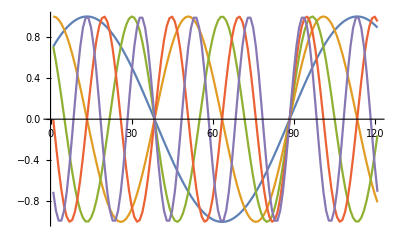

```mathematica
ListLinePlot[listXValues]
```

```mathematica
Options[HHStackLists]
```

{HHBaselineCorrection→(Mean[#1]&),HHStackIncrement→Automatic}

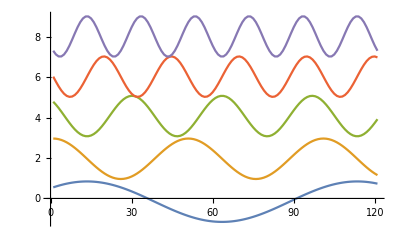

```mathematica
ListLinePlot[HHStackLists[listXValues]]
```

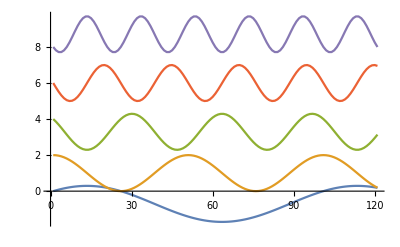

```mathematica
ListLinePlot[HHStackLists[listXValues, HHBaselineCorrection->First]]
```

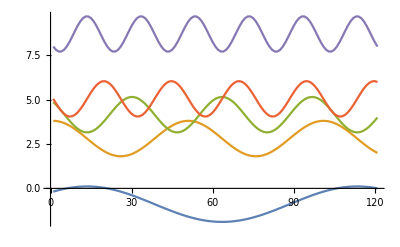

```mathematica
ListLinePlot[HHStackLists[listXValues, HHBaselineCorrection->(#[[-1]]&)]]
```

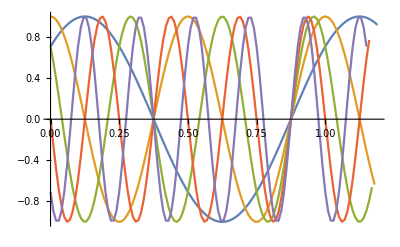

```mathematica
ListLinePlot[listXYValues]
```

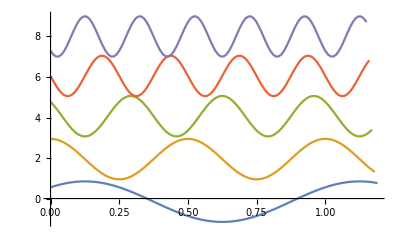

```mathematica
ListLinePlot[HHStackLists[listXYValues]]
```

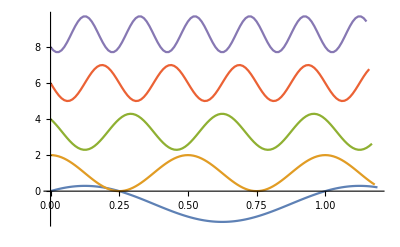

```mathematica
ListLinePlot[HHStackLists[listXYValues, HHBaselineCorrection->First]]
```

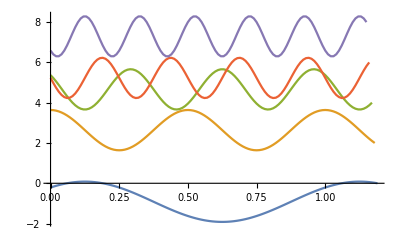

```mathematica
ListLinePlot[HHStackLists[listXYValues, HHBaselineCorrection->(#[[-1]]&)]]
```

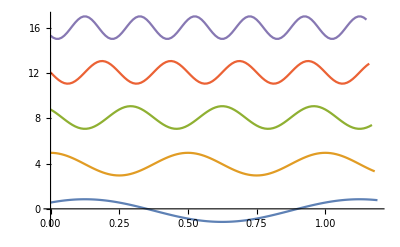

```mathematica
ListLinePlot[HHStackLists[listXYValues, HHStackIncrement->4]]
```

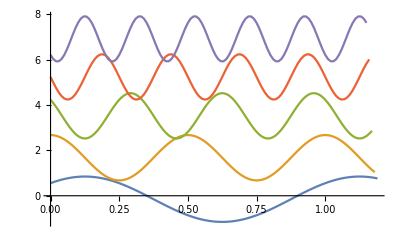

```mathematica
ListLinePlot[HHStackLists[listXYValues, HHStackIncrement->(Quantile[#-Min[#], 0.75]&)] ]
```

## HHListLinePlotStack

```mathematica
?HHListLinePlotStack
```

HHListLinePlotStack plots multiple traces together, stacked vertically.

```mathematica
Options[HHListLinePlotStack]
```

{AspectRatio→1/2,PlotRange→All,HHBaselineCorrection→(Mean[#1]&),HHStackIncrement→Automatic,AlignmentPoint→Center,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→True,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotMarkers→None,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

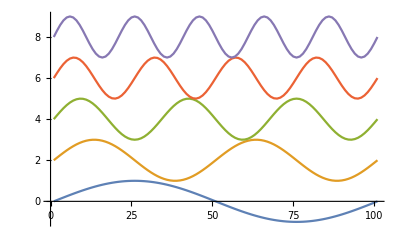

```mathematica
HHListLinePlotStack[listXValues]
```

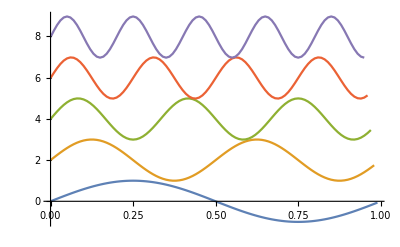

```mathematica
HHListLinePlotStack[listXYValues]
```

## Playing Around

```mathematica
HHFunctionQ[Mean]
```

False

```mathematica
HHFunctionQ[Mean[#]&]
```

True

```mathematica
HHFunctionQ[First]
```

False

```mathematica
Depth[listXValues]
```

3

```mathematica
Depth[listXYValues]
```

4

```mathematica
Dimensions /@ listXYValues
```

{{100,2},{99,2},{98,2},{97,2},{96,2}}

```mathematica
Union[(Dimensions /@ listXYValues)[[All, 2]]]
```

{2}

```mathematica
Dimensions /@ listXYValues[[All, All, 2]]
```

{{100},{99},{98},{97},{96}}

```mathematica
tempTimes=listXYValues[[All, All, 1]];
tempTraces = listXYValues[[All, All, 2]];
```

```mathematica
Dimensions[ {tempTimes, tempTraces} ]
```

{2,5}

```mathematica
{Dimensions /@ tempTimes, Dimensions /@tempTraces}
```

{{{100},{99},{98},{97},{96}},{{100},{99},{98},{97},{96}}}

```mathematica
Transpose[ {tempTimes, tempTraces}, {2, 3, 1}]
```

Transpose::tperm: Permutation {2,3,1} is longer than the dimensions {2,5} of the expression.

```mathematica
Transpose /@ MapThread[{#1, #2}&, {tempTimes, tempTraces}]
```

{{{0.,0.},{0.01,0.0627905},{0.02,0.125333},{0.03,0.187381},{0.04,0.24869},{0.05,0.309017},{0.06,0.368125},{0.07,0.425779},{0.08,0.481754},{0.09,0.535827},{0.1,0.587785},{0.11,0.637424},{0.12,0.684547},{0.13,0.728969},{0.14,0.770513},{0.15,0.809017},{0.16,0.844328},{0.17,0.876307},{0.18,0.904827},{0.19,0.929776},{0.2,0.951057},{0.21,0.968583},{0.22,0.982287},{0.23,0.992115},{0.24,0.998027},{0.25,1.},{0.26,0.998027},{0.27,0.992115},{0.28,0.982287},{0.29,0.968583},{0.3,0.951057},{0.31,0.929776},{0.32,0.904827},{0.33,0.876307},{0.34,0.844328},{0.35,0.809017},{0.36,0.770513},{0.37,0.728969},{0.38,0.684547},{0.39,0.637424},{0.4,0.587785},{0.41,0.535827},{0.42,0.481754},{0.43,0.425779},{0.44,0.368125},{0.45,0.309017},{0.46,0.24869},{0.47,0.187381},{0.48,0.125333},{0.49,0.0627905},{0.5,1.22465×10^-16},{0.51,-0.0627905},{0.52,-0.125333},{0.53,-0.187381},{0.54,-0.24869},{0.55,-0.309017},{0.56,-0.368125},{0.57,-0.425779},{0.58,-0.481754},{0.59,-0.535827},{0.6,-0.587785},{0.61,-0.637424},{0.62,-0.684547},{0.63,-0.728969},{0.64,-0.770513},{0.65,-0.809017},{0.66,-0.844328},{0.67,-0.876307},{0.68,-0.904827},{0.69,-0.929776},{0.7,-0.951057},{0.71,-0.968583},{0.72,-0.982287},{0.73,-0.992115},{0.74,-0.998027},{0.75,-1.},{0.76,-0.998027},{0.77,-0.992115},{0.78,-0.982287},{0.79,-0.968583},{0.8,-0.951057},{0.81,-0.929776},{0.82,-0.904827},{0.83,-0.876307},{0.84,-0.844328},{0.85,-0.809017},{0.86,-0.770513},{0.87,-0.728969},{0.88,-0.684547},{0.89,-0.637424},{0.9,-0.587785},{0.91,-0.535827},{0.92,-0.481754},{0.93,-0.425779},{0.94,-0.368125},{0.95,-0.309017},{0.96,-0.24869},{0.97,-0.187381},{0.98,-0.125333},{0.99,-0.0627905}},{{0.,0.},{0.01,0.125333},{0.02,0.24869},{0.03,0.368125},{0.04,0.481754},{0.05,0.587785},{0.06,0.684547},{0.07,0.770513},{0.08,0.844328},{0.09,0.904827},{0.1,0.951057},{0.11,0.982287},{0.12,0.998027},{0.13,0.998027},{0.14,0.982287},{0.15,0.951057},{0.16,0.904827},{0.17,0.844328},{0.18,0.770513},{0.19,0.684547},{0.2,0.587785},{0.21,0.481754},{0.22,0.368125},{0.23,0.24869},{0.24,0.125333},{0.25,1.22465×10^-16},{0.26,-0.125333},{0.27,-0.24869},{0.28,-0.368125},{0.29,-0.481754},{0.3,-0.587785},{0.31,-0.684547},{0.32,-0.770513},{0.33,-0.844328},{0.34,-0.904827},{0.35,-0.951057},{0.36,-0.982287},{0.37,-0.998027},{0.38,-0.998027},{0.39,-0.982287},{0.4,-0.951057},{0.41,-0.904827},{0.42,-0.844328},{0.43,-0.770513},{0.44,-0.684547},{0.45,-0.587785},{0.46,-0.481754},{0.47,-0.368125},{0.48,-0.24869},{0.49,-0.125333},{0.5,-2.44929×10^-16},{0.51,0.125333},{0.52,0.24869},{0.53,0.368125},{0.54,0.481754},{0.55,0.587785},{0.56,0.684547},{0.57,0.770513},{0.58,0.844328},{0.59,0.904827},{0.6,0.951057},{0.61,0.982287},{0.62,0.998027},{0.63,0.998027},{0.64,0.982287},{0.65,0.951057},{0.66,0.904827},{0.67,0.844328},{0.68,0.770513},{0.69,0.684547},{0.7,0.587785},{0.71,0.481754},{0.72,0.368125},{0.73,0.24869},{0.74,0.125333},{0.75,3.67394×10^-16},{0.76,-0.125333},{0.77,-0.24869},{0.78,-0.368125},{0.79,-0.481754},{0.8,-0.587785},{0.81,-0.684547},{0.82,-0.770513},{0.83,-0.844328},{0.84,-0.904827},{0.85,-0.951057},{0.86,-0.982287},{0.87,-0.998027},{0.88,-0.998027},{0.89,-0.982287},{0.9,-0.951057},{0.91,-0.904827},{0.92,-0.844328},{0.93,-0.770513},{0.94,-0.684547},{0.95,-0.587785},{0.96,-0.481754},{0.97,-0.368125},{0.98,-0.24869}},{{0.,0.},{0.01,0.187381},{0.02,0.368125},{0.03,0.535827},{0.04,0.684547},{0.05,0.809017},{0.06,0.904827},{0.07,0.968583},{0.08,0.998027},{0.09,0.992115},{0.1,0.951057},{0.11,0.876307},{0.12,0.770513},{0.13,0.637424},{0.14,0.481754},{0.15,0.309017},{0.16,0.125333},{0.17,-0.0627905},{0.18,-0.24869},{0.19,-0.425779},{0.2,-0.587785},{0.21,-0.728969},{0.22,-0.844328},{0.23,-0.929776},{0.24,-0.982287},{0.25,-1.},{0.26,-0.982287},{0.27,-0.929776},{0.28,-0.844328},{0.29,-0.728969},{0.3,-0.587785},{0.31,-0.425779},{0.32,-0.24869},{0.33,-0.0627905},{0.34,0.125333},{0.35,0.309017},{0.36,0.481754},{0.37,0.637424},{0.38,0.770513},{0.39,0.876307},{0.4,0.951057},{0.41,0.992115},{0.42,0.998027},{0.43,0.968583},{0.44,0.904827},{0.45,0.809017},{0.46,0.684547},{0.47,0.535827},{0.48,0.368125},{0.49,0.187381},{0.5,3.67394×10^-16},{0.51,-0.187381},{0.52,-0.368125},{0.53,-0.535827},{0.54,-0.684547},{0.55,-0.809017},{0.56,-0.904827},{0.57,-0.968583},{0.58,-0.998027},{0.59,-0.992115},{0.6,-0.951057},{0.61,-0.876307},{0.62,-0.770513},{0.63,-0.637424},{0.64,-0.481754},{0.65,-0.309017},{0.66,-0.125333},{0.67,0.0627905},{0.68,0.24869},{0.69,0.425779},{0.7,0.587785},{0.71,0.728969},{0.72,0.844328},{0.73,0.929776},{0.74,0.982287},{0.75,1.},{0.76,0.982287},{0.77,0.929776},{0.78,0.844328},{0.79,0.728969},{0.8,0.587785},{0.81,0.425779},{0.82,0.24869},{0.83,0.0627905},{0.84,-0.125333},{0.85,-0.309017},{0.86,-0.481754},{0.87,-0.637424},{0.88,-0.770513},{0.89,-0.876307},{0.9,-0.951057},{0.91,-0.992115},{0.92,-0.998027},{0.93,-0.968583},{0.94,-0.904827},{0.95,-0.809017},{0.96,-0.684547},{0.97,-0.535827}},{{0.,0.},{0.01,0.24869},{0.02,0.481754},{0.03,0.684547},{0.04,0.844328},{0.05,0.951057},{0.06,0.998027},{0.07,0.982287},{0.08,0.904827},{0.09,0.770513},{0.1,0.587785},{0.11,0.368125},{0.12,0.125333},{0.13,-0.125333},{0.14,-0.368125},{0.15,-0.587785},{0.16,-0.770513},{0.17,-0.904827},{0.18,-0.982287},{0.19,-0.998027},{0.2,-0.951057},{0.21,-0.844328},{0.22,-0.684547},{0.23,-0.481754},{0.24,-0.24869},{0.25,-2.44929×10^-16},{0.26,0.24869},{0.27,0.481754},{0.28,0.684547},{0.29,0.844328},{0.3,0.951057},{0.31,0.998027},{0.32,0.982287},{0.33,0.904827},{0.34,0.770513},{0.35,0.587785},{0.36,0.368125},{0.37,0.125333},{0.38,-0.125333},{0.39,-0.368125},{0.4,-0.587785},{0.41,-0.770513},{0.42,-0.904827},{0.43,-0.982287},{0.44,-0.998027},{0.45,-0.951057},{0.46,-0.844328},{0.47,-0.684547},{0.48,-0.481754},{0.49,-0.24869},{0.5,-4.89859×10^-16},{0.51,0.24869},{0.52,0.481754},{0.53,0.684547},{0.54,0.844328},{0.55,0.951057},{0.56,0.998027},{0.57,0.982287},{0.58,0.904827},{0.59,0.770513},{0.6,0.587785},{0.61,0.368125},{0.62,0.125333},{0.63,-0.125333},{0.64,-0.368125},{0.65,-0.587785},{0.66,-0.770513},{0.67,-0.904827},{0.68,-0.982287},{0.69,-0.998027},{0.7,-0.951057},{0.71,-0.844328},{0.72,-0.684547},{0.73,-0.481754},{0.74,-0.24869},{0.75,-7.34788×10^-16},{0.76,0.24869},{0.77,0.481754},{0.78,0.684547},{0.79,0.844328},{0.8,0.951057},{0.81,0.998027},{0.82,0.982287},{0.83,0.904827},{0.84,0.770513},{0.85,0.587785},{0.86,0.368125},{0.87,0.125333},{0.88,-0.125333},{0.89,-0.368125},{0.9,-0.587785},{0.91,-0.770513},{0.92,-0.904827},{0.93,-0.982287},{0.94,-0.998027},{0.95,-0.951057},{0.96,-0.844328}},{{0.,0.},{0.01,0.309017},{0.02,0.587785},{0.03,0.809017},{0.04,0.951057},{0.05,1.},{0.06,0.951057},{0.07,0.809017},{0.08,0.587785},{0.09,0.309017},{0.1,1.22465×10^-16},{0.11,-0.309017},{0.12,-0.587785},{0.13,-0.809017},{0.14,-0.951057},{0.15,-1.},{0.16,-0.951057},{0.17,-0.809017},{0.18,-0.587785},{0.19,-0.309017},{0.2,-2.44929×10^-16},{0.21,0.309017},{0.22,0.587785},{0.23,0.809017},{0.24,0.951057},{0.25,1.},{0.26,0.951057},{0.27,0.809017},{0.28,0.587785},{0.29,0.309017},{0.3,3.67394×10^-16},{0.31,-0.309017},{0.32,-0.587785},{0.33,-0.809017},{0.34,-0.951057},{0.35,-1.},{0.36,-0.951057},{0.37,-0.809017},{0.38,-0.587785},{0.39,-0.309017},{0.4,-4.89859×10^-16},{0.41,0.309017},{0.42,0.587785},{0.43,0.809017},{0.44,0.951057},{0.45,1.},{0.46,0.951057},{0.47,0.809017},{0.48,0.587785},{0.49,0.309017},{0.5,6.12323×10^-16},{0.51,-0.309017},{0.52,-0.587785},{0.53,-0.809017},{0.54,-0.951057},{0.55,-1.},{0.56,-0.951057},{0.57,-0.809017},{0.58,-0.587785},{0.59,-0.309017},{0.6,-7.34788×10^-16},{0.61,0.309017},{0.62,0.587785},{0.63,0.809017},{0.64,0.951057},{0.65,1.},{0.66,0.951057},{0.67,0.809017},{0.68,0.587785},{0.69,0.309017},{0.7,-2.69546×10^-15},{0.71,-0.309017},{0.72,-0.587785},{0.73,-0.809017},{0.74,-0.951057},{0.75,-1.},{0.76,-0.951057},{0.77,-0.809017},{0.78,-0.587785},{0.79,-0.309017},{0.8,-9.79717×10^-16},{0.81,0.309017},{0.82,0.587785},{0.83,0.809017},{0.84,0.951057},{0.85,1.},{0.86,0.951057},{0.87,0.809017},{0.88,0.587785},{0.89,0.309017},{0.9,1.10218×10^-15},{0.91,-0.309017},{0.92,-0.587785},{0.93,-0.809017},{0.94,-0.951057},{0.95,-1.}}}